```mathematica
M=5;
beta=0.1;
g=0.;
alpha=0.5;
l=0.9;
rz=0.5;
L=3.0;
epsilon=Exp[-2*L];
bVal=1-2*epsilon;
r=2*L*rz;

xi[z_,Delta_,OmegaA_,sign_]=M*(sign*Delta*z+OmegaA)

betaA=alpha+beta-1-xi^2

betaZ=Together[beta+2*alpha+2*alpha^2*(xi^4+2*g*xi^3+2*g^2*xi^2-5*xi^2-6*g*xi+3)/((xi^2-1)*(xi^4-6*xi^2-4*g*xi+3))]

nBetaZ=Numerator[betaZ]

dBetaZ=Denominator[betaZ]

q[z_,Delta_,OmegaA_]=((1-l)*nBetaZ+l*betaA*dBetaZ)/nBetaZ
F[z_,Delta_,OmegaA_]=(Sqrt[-q[z,Delta,OmegaA]/. xi->xi[z,Delta,OmegaA,1]]+Sqrt[-q[z,Delta,OmegaA]/. xi->xi[z,Delta,OmegaA,-1]])/(-z^2+1)
```

5 (OmegaA+Delta sign z)

-0.4-xi^2

(1.1 (-1.63636+6.72727 xi^2-6.54545 xi^4+1. xi^6))/((-1.+xi^2) (3.-6. xi^2+xi^4))

1.1 (-1.63636+6.72727 xi^2-6.54545 xi^4+1. xi^6)

(-1.+xi^2) (3.-6. xi^2+xi^4)

(0.909091 (0.9 (-0.4-xi^2) (-1.+xi^2) (3.-6. xi^2+xi^4)+0.11 (-1.63636+6.72727 xi^2-6.54545 xi^4+1. xi^6)))/(-1.63636+6.72727 xi^2-6.54545 xi^4+1. xi^6)

1/(1-z^2)(0.953463 √(-((0.9 (-0.4-25 (OmegaA-Delta z)^2) (-1.+25 (OmegaA-Delta z)^2) (3.-150. (OmegaA-Delta z)^2+625 (OmegaA-Delta z)^4)+0.11 (-1.63636+168.182 (OmegaA-Delta z)^2-4090.91 (OmegaA-Delta z)^4+15625. (OmegaA-Delta z)^6))/(-1.63636+168.182 (OmegaA-Delta z)^2-4090.91 (OmegaA-Delta z)^4+15625. (OmegaA-Delta z)^6)))+0.953463 √(-((0.9 (-0.4-25 (OmegaA+Delta z)^2) (-1.+25 (OmegaA+Delta z)^2) (3.-150. (OmegaA+Delta z)^2+625 (OmegaA+Delta z)^4)+0.11 (-1.63636+168.182 (OmegaA+Delta z)^2-4090.91 (OmegaA+Delta z)^4+15625. (OmegaA+Delta z)^6))/(-1.63636+168.182 (OmegaA+Delta z)^2-4090.91 (OmegaA+Delta z)^4+15625. (OmegaA+Delta z)^6))))

```mathematica
LogSpace[start_,end_,steps_]:=Exp[Range[Log[start],Log[end],(Log[end]-Log[start])/steps]]

deltaValues=LogSpace[0.01,1,99]
initialOmega=0.+0.07464607515065497 ⅈ;  (*Initial guess for the first Delta*)
omegaValues=Table[initialOmega=OmegaA/. FindRoot[NIntegrate[F[z,Delta,OmegaA],{z,0,bVal}]==r,{OmegaA,initialOmega}],{Delta,deltaValues}]
```

{0.01,0.0104762,0.010975,0.0114976,0.012045,0.0126186,0.0132194,0.0138489,0.0145083,0.0151991,0.0159228,0.016681,0.0174753,0.0183074,0.0191791,0.0200923,0.021049,0.0220513,0.0231013,0.0242013,0.0253536,0.0265609,0.0278256,0.0291505,0.0305386,0.0319927,0.033516,0.0351119,0.0367838,0.0385353,0.0403702,0.0422924,0.0443062,0.0464159,0.048626,0.0509414,0.053367,0.0559081,0.0585702,0.0613591,0.0642807,0.0673415,0.070548,0.0739072,0.0774264,0.0811131,0.0849753,0.0890215,0.0932603,0.097701,0.102353,0.107227,0.112332,0.117681,0.123285,0.129155,0.135305,0.141747,0.148497,0.155568,0.162975,0.170735,0.178865,0.187382,0.196304,0.205651,0.215443,0.225702,0.236449,0.247708,0.259502,0.271859,0.284804,0.298365,0.312572,0.327455,0.343047,0.359381,0.376494,0.394421,0.413201,0.432876,0.453488,0.475081,0.497702,0.521401,0.546228,0.572237,0.599484,0.628029,0.657933,0.689261,0.722081,0.756463,0.792483,0.830218,0.869749,0.911163,0.954548,1.}

NIntegrate::inumr: The integrand (0.953463 √(-(0.9 Plus[«2»] Plus[«2»] Plus[«3»]+0.11 Plus[«4»])/(-1.63636+Times[«2»]+Times[«2»]+Times[«2»]))+0.953463 √(-(0.9 Plus[«2»] Plus[«2»] Plus[«3»]+«20» «1»)/(-1.63636+Times[«2»]+«1»+Times[«2»])))/(1-z^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.995042}}.

NIntegrate::inumr: The integrand ((0.476731 (((0.9 Plus[«2»] Plus[«2»] Plus[«3»]+«20» «1») «1»)/(-«19»+«2»+Times[«2»])^2-(«1»)/(-«19»+«2»+«1»)))/(√(-(0.9 Plus[«2»] Plus[«2»] Plus[«3»]+0.11 «1»)/(-1.63636+Times[«2»]+Times[«2»]+Times[«2»])))+(«19» ((«1»)/(«1»)-«1»))/(√(-(«1»«1»«1»)/(«1»))))/(1-z^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.995042}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.888138}. NIntegrate obtained 10.6698+0. ⅈ and 0.0195752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.233198}. NIntegrate obtained 10.6787+0. ⅈ and 0.000140838 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.888138}. NIntegrate obtained 10.6782+0. ⅈ and 0.00154775 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.+0.0746461 ⅈ,0.+0.0747066 ⅈ,0.+0.074773 ⅈ,0.+0.0748458 ⅈ,0.+0.0749257 ⅈ,0.+0.0750133 ⅈ,0.+0.0751093 ⅈ,0.+0.0752145 ⅈ,0.+0.0753299 ⅈ,0.+0.0754564 ⅈ,0.+0.075595 ⅈ,0.+0.0757469 ⅈ,0.+0.0759133 ⅈ,0.+0.0760956 ⅈ,0.+0.0762953 ⅈ,0.+0.0765139 ⅈ,0.+0.0767533 ⅈ,0.+0.0770153 ⅈ,0.+0.077302 ⅈ,0.+0.0776156 ⅈ,0.+0.0779585 ⅈ,0.+0.0783334 ⅈ,0.+0.078743 ⅈ,0.+0.0791905 ⅈ,0.+0.079679 ⅈ,0.+0.0802121 ⅈ,0.+0.0807936 ⅈ,0.+0.0814274 ⅈ,0.+0.0821178 ⅈ,0.+0.0828694 ⅈ,0.+0.083687 ⅈ,0.+0.0845758 ⅈ,0.+0.0855412 ⅈ,0.+0.0865891 ⅈ,0.+0.0877255 ⅈ,0.+0.0889569 ⅈ,0.+0.0902903 ⅈ,0.+0.0917332 ⅈ,0.+0.0932937 ⅈ,0.+0.0949807 ⅈ,0.+0.0968039 ⅈ,0.+0.0987747 ⅈ,0.+0.100906 ⅈ,0.+0.103212 ⅈ,0.+0.10571 ⅈ,0.+0.108423 ⅈ,0.+0.111374 ⅈ,0.+0.114766 ⅈ,0.+0.119005 ⅈ,0.+0.124143 ⅈ,0.+0.130394 ⅈ,0.+0.138118 ⅈ,0.+0.147896 ⅈ,0.+0.16071 ⅈ,0.+0.178378 ⅈ,0.+0.204801 ⅈ,0.+0.251007 ⅈ,0.+0.383093 ⅈ,0.+0.900455 ⅈ,0.+0.897904 ⅈ,0.+0.895049 ⅈ,0.+0.891902 ⅈ,0.+0.888468 ⅈ,0.+0.884536 ⅈ,0.+0.880253 ⅈ,0.+0.875691 ⅈ,0.+0.870265 ⅈ,0.+0.864568 ⅈ,0.+0.858039 ⅈ,0.+0.850693 ⅈ,0.+0.842815 ⅈ,0.+0.833716 ⅈ,0.+0.823531 ⅈ,0.+0.811813 ⅈ,0.+0.79855 ⅈ,0.+0.783483 ⅈ,0.+0.766129 ⅈ,0.+0.746344 ⅈ,0.+0.722634 ⅈ,0.+0.693711 ⅈ,0.+0.658456 ⅈ,0.+0.61131 ⅈ,0.+0.541777 ⅈ,0.-0.341935 ⅈ,0.-0.243314 ⅈ,0.-0.000090422 ⅈ,0.-0.0000880294 ⅈ,0.-1.60255×10^-15 ⅈ,0.+1.59918×10^-6 ⅈ,0.+1.69809×10^-15 ⅈ,0.+1.69809×10^-15 ⅈ,0.-0.159793 ⅈ,0.-0.166066 ⅈ,0.-0.172638 ⅈ,0.-0.179249 ⅈ,0.-0.185811 ⅈ,0.-0.192254 ⅈ,0.-0.198668 ⅈ,0.-0.204799 ⅈ,-1.74967×10^-15-0.210689 ⅈ}

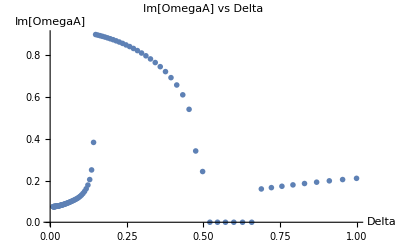

```mathematica
combinedValues=Transpose[{deltaValues,omegaValues}];
ListPlot[Transpose[{deltaValues,Abs[Im[omegaValues]]}],PlotStyle->PointSize[0.01],Joined->False,PlotRange->All,AxesLabel->{"Delta","Im[OmegaA]"},PlotLabel->"Im[OmegaA] vs Delta"]
```

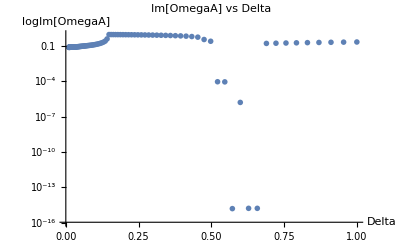

```mathematica
ListLogPlot[Transpose[{deltaValues,Abs[Im[omegaValues]]}],PlotStyle->PointSize[0.01],Joined->False,PlotRange->All,AxesLabel->{"Delta","logIm[OmegaA]"},PlotLabel->"Im[OmegaA] vs Delta"]
```

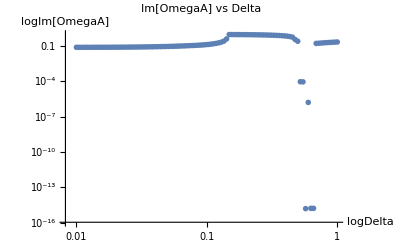

```mathematica
ListLogLogPlot[Transpose[{deltaValues,Abs[Im[omegaValues]]}],PlotStyle->PointSize[0.01],Joined->False,PlotRange->All,AxesLabel->{"logDelta","logIm[OmegaA]"},PlotLabel->"Im[OmegaA] vs Delta"]
```

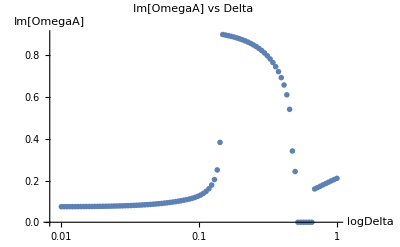

```mathematica
ListLogLinearPlot[Transpose[{deltaValues,Abs[Im[omegaValues]]}],PlotStyle->PointSize[0.01],Joined->False,PlotRange->All,AxesLabel->{"logDelta","Im[OmegaA]"},PlotLabel->"Im[OmegaA] vs Delta"]
```

```mathematica
Do[Print[combinedValues[[i]]],{i,Length[combinedValues]}]
```

{0.01,0.+0.0746461 ⅈ}

{0.0104762,0.+0.0747066 ⅈ}

{0.010975,0.+0.074773 ⅈ}

{0.0114976,0.+0.0748458 ⅈ}

{0.012045,0.+0.0749257 ⅈ}

{0.0126186,0.+0.0750133 ⅈ}

{0.0132194,0.+0.0751093 ⅈ}

{0.0138489,0.+0.0752145 ⅈ}

{0.0145083,0.+0.0753299 ⅈ}

{0.0151991,0.+0.0754564 ⅈ}

{0.0159228,0.+0.075595 ⅈ}

{0.016681,0.+0.0757469 ⅈ}

{0.0174753,0.+0.0759133 ⅈ}

{0.0183074,0.+0.0760956 ⅈ}

{0.0191791,0.+0.0762953 ⅈ}

{0.0200923,0.+0.0765139 ⅈ}

{0.021049,0.+0.0767533 ⅈ}

{0.0220513,0.+0.0770153 ⅈ}

{0.0231013,0.+0.077302 ⅈ}

{0.0242013,0.+0.0776156 ⅈ}

{0.0253536,0.+0.0779585 ⅈ}

{0.0265609,0.+0.0783334 ⅈ}

{0.0278256,0.+0.078743 ⅈ}

{0.0291505,0.+0.0791905 ⅈ}

{0.0305386,0.+0.079679 ⅈ}

{0.0319927,0.+0.0802121 ⅈ}

{0.033516,0.+0.0807936 ⅈ}

{0.0351119,0.+0.0814274 ⅈ}

{0.0367838,0.+0.0821178 ⅈ}

{0.0385353,0.+0.0828694 ⅈ}

{0.0403702,0.+0.083687 ⅈ}

{0.0422924,0.+0.0845758 ⅈ}

{0.0443062,0.+0.0855412 ⅈ}

{0.0464159,0.+0.0865891 ⅈ}

{0.048626,0.+0.0877255 ⅈ}

{0.0509414,0.+0.0889569 ⅈ}

{0.053367,0.+0.0902903 ⅈ}

{0.0559081,0.+0.0917332 ⅈ}

{0.0585702,0.+0.0932937 ⅈ}

{0.0613591,0.+0.0949807 ⅈ}

{0.0642807,0.+0.0968039 ⅈ}

{0.0673415,0.+0.0987747 ⅈ}

{0.070548,0.+0.100906 ⅈ}

{0.0739072,0.+0.103212 ⅈ}

{0.0774264,0.+0.10571 ⅈ}

{0.0811131,0.+0.108423 ⅈ}

{0.0849753,0.+0.111374 ⅈ}

{0.0890215,0.+0.114766 ⅈ}

{0.0932603,0.+0.119005 ⅈ}

{0.097701,0.+0.124143 ⅈ}

{0.102353,0.+0.130394 ⅈ}

{0.107227,0.+0.138118 ⅈ}

{0.112332,0.+0.147896 ⅈ}

{0.117681,0.+0.16071 ⅈ}

{0.123285,0.+0.178378 ⅈ}

{0.129155,0.+0.204801 ⅈ}

{0.135305,0.+0.251007 ⅈ}

{0.141747,0.+0.383093 ⅈ}

{0.148497,0.+0.900455 ⅈ}

{0.155568,0.+0.897904 ⅈ}

{0.162975,0.+0.895049 ⅈ}

{0.170735,0.+0.891902 ⅈ}

{0.178865,0.+0.888468 ⅈ}

{0.187382,0.+0.884536 ⅈ}

{0.196304,0.+0.880253 ⅈ}

{0.205651,0.+0.875691 ⅈ}

{0.215443,0.+0.870265 ⅈ}

{0.225702,0.+0.864568 ⅈ}

{0.236449,0.+0.858039 ⅈ}

{0.247708,0.+0.850693 ⅈ}

{0.259502,0.+0.842815 ⅈ}

{0.271859,0.+0.833716 ⅈ}

{0.284804,0.+0.823531 ⅈ}

{0.298365,0.+0.811813 ⅈ}

{0.312572,0.+0.79855 ⅈ}

{0.327455,0.+0.783483 ⅈ}

{0.343047,0.+0.766129 ⅈ}

{0.359381,0.+0.746344 ⅈ}

{0.376494,0.+0.722634 ⅈ}

{0.394421,0.+0.693711 ⅈ}

{0.413201,0.+0.658456 ⅈ}

{0.432876,0.+0.61131 ⅈ}

{0.453488,0.+0.541777 ⅈ}

{0.475081,0.-0.341935 ⅈ}

{0.497702,0.-0.243314 ⅈ}

{0.521401,0.-0.000090422 ⅈ}

{0.546228,0.-0.0000880294 ⅈ}

{0.572237,0.-1.60255×10^-15 ⅈ}

{0.599484,0.+1.59918×10^-6 ⅈ}

{0.628029,0.+1.69809×10^-15 ⅈ}

{0.657933,0.+1.69809×10^-15 ⅈ}

{0.689261,0.-0.159793 ⅈ}

{0.722081,0.-0.166066 ⅈ}

{0.756463,0.-0.172638 ⅈ}

{0.792483,0.-0.179249 ⅈ}

{0.830218,0.-0.185811 ⅈ}

{0.869749,0.-0.192254 ⅈ}

{0.911163,0.-0.198668 ⅈ}

{0.954548,0.-0.204799 ⅈ}

{1.,-1.74967×10^-15-0.210689 ⅈ}